```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,t_]:=-x;
f1[x1_,x2_,t_]:= x2;
f2[x1_,x2_,t_]:= -x1;

(*Error message*)
euler::nonnegativeint = "Nmax must be a non-negative integer";

euler[dt_,Nmax_,a1_,a2_]:= Module[{j = 0,n,x1,x2,t},If[Or[Nmax≤ 0,Not[IntegerQ[Nmax]]],Message[euler::nonnegativeint],x1[0]:=a1;x2[0]:= a2;x1[j_]:=(x1[j] = x1[j-1]+dt f1[x1[j-1],x2[j-1],t]);x2[j_] := (x2[j] = x2[j-1]+dt f2[x1[j-1],x2[j-1],t]);Table[{j dt,x1[j]},{j,0,Nmax}]
]
];


euler[.1,10,1,2]
```

{{0.,1},{0.1,1.2},{0.2,1.39},{0.3,1.568},{0.4,1.7321},{0.5,1.88052},{0.6,2.01162},{0.7,2.12391},{0.8,2.21609},{0.9,2.28703},{1.,2.33581}}

```mathematica
{{0.,1},{0.1,1.2},{0.2,1.39},{0.30000000000000004,1.5679999999999998},{0.4,1.7320999999999998},{0.5,1.8805199999999997},{0.6000000000000001,2.0116189999999996},{0.7000000000000001,2.1239127999999994},{0.8,2.216090409999999},{0.9,2.287028891999999},{1.,2.335806469899999}}
```

{{0.,1},{0.1,1.2},{0.2,1.39},{0.3,1.568},{0.4,1.7321},{0.5,1.88052},{0.6,2.01162},{0.7,2.12391},{0.8,2.21609},{0.9,2.28703},{1.,2.33581}}

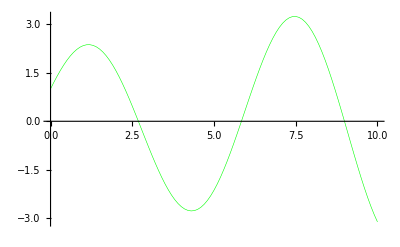

```mathematica
eulergraph[dt_,Nmax_,a1_,a2_]:= ListLinePlot[euler[dt,Nmax,a1,a2],PlotStyle->{Thickness[0.001],RGBColor[0,1,0]},PlotRange->All];
eulergraph[.1,100,1,2]
```

```mathematica
asol[a1_,a2_] := DSolve[{x''[t] == f[x[t],t],x[0] == a1,x'[0] == a2},x[t],t];
asol[1,2]
```

{{x[t]→Cos[t]+2 Sin[t]}}

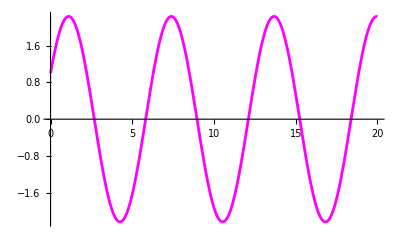

```mathematica
agraph[a1_,a2_,tlast_]:= Plot[Evaluate[x[t]/.asol[a1,a2]],{t,0,tlast},PlotStyle->{Thickness[0.005],RGBColor[1,0,1]},PlotRange->All];agraph[1,2,20]
```

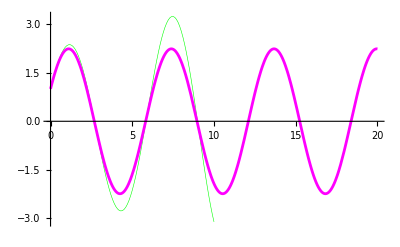

```mathematica
Show[eulergraph[.1,100,1,2],agraph[1,2,20]]
```

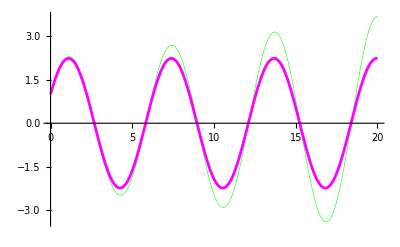

```mathematica
Show[eulergraph[0.05,400,1,2],agraph[1,2,20]]
```

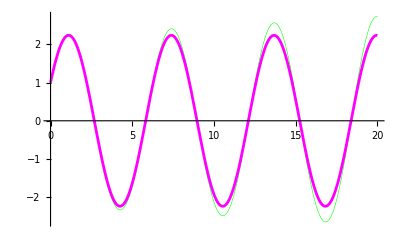

```mathematica
Show[eulergraph[0.02,1000,1,2],agraph[1,2,20]]
```

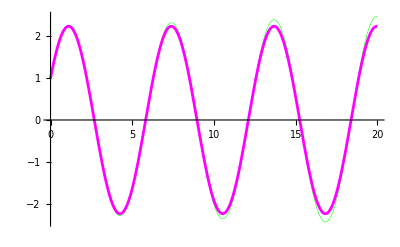

```mathematica
Show[eulergraph[0.01,2000,1,2],agraph[1,2,20]]
```